```mathematica
ff[z_] = (1-z)(1+z+z^2-(μ^2z^3)/4)  ;
At00[z_] = (1-z)μ;
```

```mathematica
AxEqn=Ax[z] (w^2/f[z]- z^2 At0'[z]^2)+Ax'[z] f'[z]+f[z] Ax''[z];
```

```mathematica
AA[z_] = f[z]^(-I w/T) S[z] ;
```

```mathematica
AxEEE[w_,μ_] = Simplify[AxEqn/f[z]^(-I w/T) /. Ax -> AA]/. At0 -> At00 /. f -> ff /. T->(3-μ^2/4) ;
```

```mathematica
Ser1[z_,w_,μ_] = 1 + a (z-1) + b (z-1)^2 + c (z-1)^3 ;
SS[z_] = Ser1[z,w,μ];
```

```mathematica
aa = Simplify[Solve[Simplify[Series[AxEEE[w,μ] /. S -> SS,{z,1,0}]]==0,a]][[1]]
```

{a→(4 (μ^2+(48 w^2 (-4+μ^2))/((-12+μ^2)^2)-(6 ⅈ w (-4+μ^2))/(-12+μ^2)))/(-12+8 ⅈ w+μ^2)}

```mathematica
bb = Simplify[Solve[Simplify[Series[AxEEE[w,μ] /. S -> SS /. aa,{z,1,1}]]==0,b]][[1]]
```

{b→-(2 w (-4608 w^3 (-4+μ^2)^2+12 w (-12+μ^2)^2 (336-56 μ^2+5 μ^4)+ⅈ (-12+μ^2)^3 (-144-72 μ^2+31 μ^4)+96 ⅈ w^2 (-4032+2160 μ^2-404 μ^4+21 μ^6)))/((-12+μ^2)^4 (-32 w^2+12 ⅈ w (-12+μ^2)+(-12+μ^2)^2))}

```mathematica
cc = Simplify[Solve[Simplify[Series[AxEEE[w,μ] /. S -> SS /. aa /. bb,{z,1,2}]]==0,c]][[1]]
```

{c→(4 w (442368 w^5 (-4+μ^2)^3+3 ⅈ (-12+μ^2)^5 (576+48 μ^2+76 μ^4+25 μ^6)-48 w (-12+μ^2)^4 (1824-128 μ^2-118 μ^4+27 μ^6)+48 ⅈ w^2 (-12+μ^2)^3 (-28224+9264 μ^2-924 μ^4+109 μ^6)-256 w^3 (-12+μ^2)^2 (-35136+19056 μ^2-4284 μ^4+445 μ^6)-27648 ⅈ w^4 (11520-8832 μ^2+2624 μ^4-344 μ^6+15 μ^8)))/(3 (-12+μ^2)^6 (-256 ⅈ w^3-192 w^2 (-12+μ^2)+44 ⅈ w (-12+μ^2)^2+3 (-12+μ^2)^3))}

```mathematica
Ser2[z_,w_,μ_]  = Ser1[z,w,μ] /. aa /. bb /. cc;
```

```mathematica
ep = 0.0001;
```

```mathematica
SerPr2[z_,w_,μ_]=D[Ser2[z,w,μ],z];
```

```mathematica
soln2[w_,μ_] :=NDSolve[{AxEEE[w,μ]==0,S[1-ep]== Ser2[1-ep,w,μ],S'[1-ep]==SerPr2[1-ep,w,μ]},S,{z,0+ep/10,1-ep}]
```

```mathematica
S[0.1] /.soln2[2,1][[1]][[1]]
```

0.244998-0.974364 ⅈ

```mathematica
σ[w_,μ_] := -I/w S'[ep/10]/S[ep/10]/.soln2[w,μ][[1]][[1]]
```

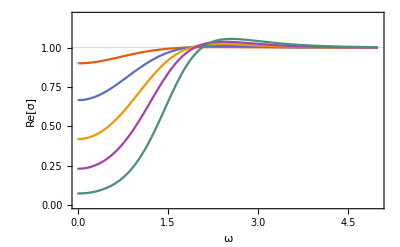

```mathematica
Plot[{Re[σ[w ,0.4]],Re[σ[w ,0.8]],Re[σ[w ,1.2]],Re[σ[w ,1.6]],Re[σ[w ,2.2]]},{w,0,5},GridLines->{{},{1}},PlotRange -> {0,1.2},Frame -> True, Axes -> False,FrameLabel -> {"ω","Re[σ]"},RotateLabel -> False, LabelStyle -> 13, PlotTheme->"Scientific"]
```

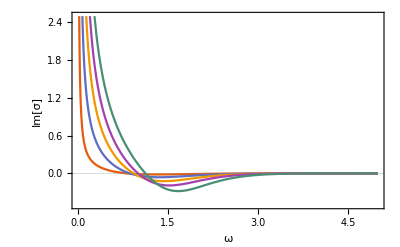

```mathematica
Plot[{Im[σ[w ,0.4]],Im[σ[w ,0.8]],Im[σ[w ,1.2]],Im[σ[w ,1.6]],Im[σ[w ,2.2]]},{w,0,5},GridLines->{{},{0}},PlotRange -> {-0.5,2.5},Frame -> True, Axes -> False,FrameLabel -> {"ω","Im[σ]"},RotateLabel -> False, LabelStyle -> 13, PlotTheme->"Scientific"]
```